```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}];
(*fileName = "~/Downloads/optimizerHistory.json";*)
```

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

```mathematica
runningBest = FoldList[Max,First[#],Rest[#]]&[raw[[All,"maximizeMe"]]];
```

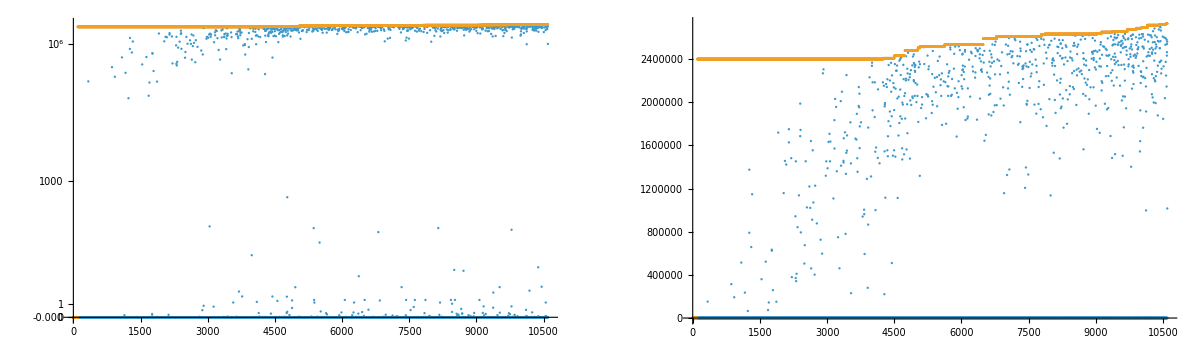

```mathematica
GraphicsGrid[{{
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

S1ELkG : 1014.8882471261
S2ELkG : -4384.7865221453
S3ELkG : -245.0673708616
S1EL_xOffset : 0.0006987038
S1EL_yOffset : 0.0001731053
S2EL_xOffset : 0.0005410284
S2EL_yOffset : 0.0000786965
S2ER_xOffset : 0.000262815
S2ER_yOffset : -0.0001495286
S1ER_xOffset : 0.0004088656
S1ER_yOffset : -0.0008969899
XC1FFkG : 0.0565491296
XC3FFkG : -0.030158801
YC1FFkG : -0.0093707882
YC2FFkG : 0.0664008807
PDrive_median_x : -9.0992e-6
PDrive_median_y : -3.612e-6
PDrive_median_xp : 0.0001106937
PDrive_median_yp : 0.0002649414
PDrive_median_energy : 9.777503948342046738e9
PDrive_sigmaSI90_x : 0.000027145
PDrive_sigmaSI90_y : 0.0000128391
PDrive_sigmaSI90_z : 9.3779e-6
PDrive_fitSigma_x : 0.0000276589
PDrive_fitSigma_y : 0.0000122211
PDrive_fitSigma_z : 3.9573e-6
PDrive_sigmaSI90_xp : 0.0003847663
PDrive_sigmaSI90_yp : 0.000033976
PDrive_sigmaSI90_energy : 8.2357724653728753e7
PDrive_emitSI90_x : 0.000203583
PDrive_emitSI90_y : 7.5235e-6
PDrive_norm_emit_x : 0.0001078559
PDrive_norm_emit_y : 4.638e-6
PDrive_charge_nC : 1.58832
PDrive_BMAG_x : 2.1620714987
PDrive_BMAG_y : 1.5390644964
PDrive_sliced_BMAG_x : List(2.034264498,3.7303695392,1.6759325953,2.9591493723,4.4542830687)
PDrive_sliced_BMAG_y : List(2.0774508836,2.9256899578,3.4311791923,2.6973752337,2.6717333695)
lostChargeFraction : 0.0073
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
PDrive_rms100_x : 0.0000345618
PDrive_rms100_y : 0.0000157323
PDrive_rms100_z : 0.0000103312
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 3.2988e-6
maximizeMe : 2.7282749578075465e6
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : True

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{S1ELkG,S2ELkG,S3ELkG,S1EL_xOffset,S1EL_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S1ER_xOffset,S1ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

## Plot specific

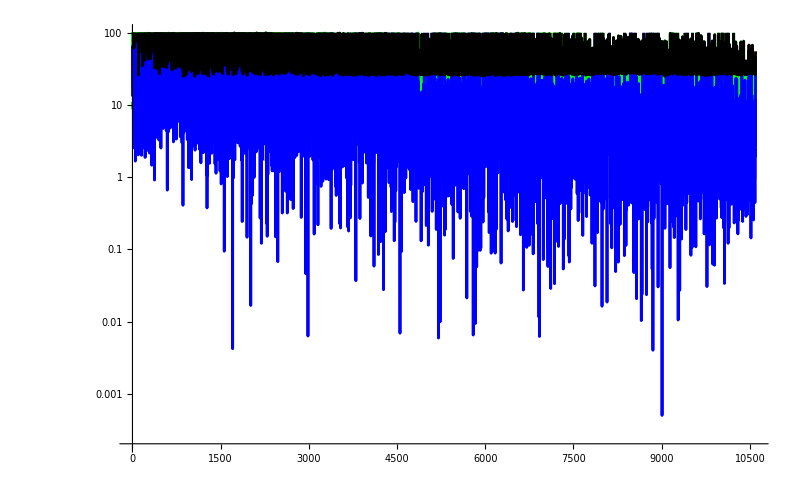

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PDrive_fitSigma_x","PDrive_fitSigma_y","PDrive_fitSigma_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,
PlotRange->{All,50},
(*PlotRange->{{-35,-21},{-50,-30},{All,50}},*)
Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"]&&MemberQ[Keys[raw[[1]]],"PWitness_sigmaSI90_z"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
#["maximizeMe"]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",
InterpolationOrder->0,
(*PlotRange->{1*^5,All},*)
PlotRange->{{-35,-21},{-50,-30},{1*^5,All}},
Mesh->All,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"maximizeMe",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]
]
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

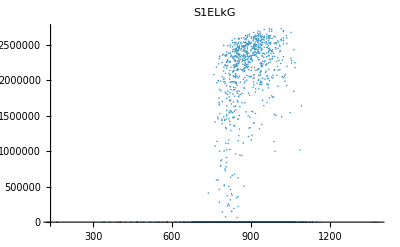
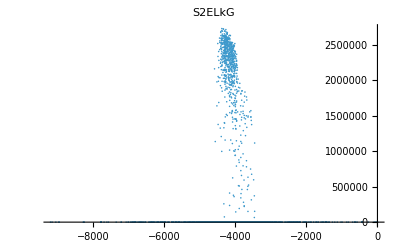
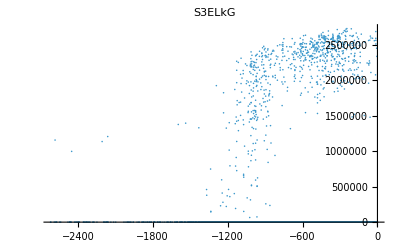
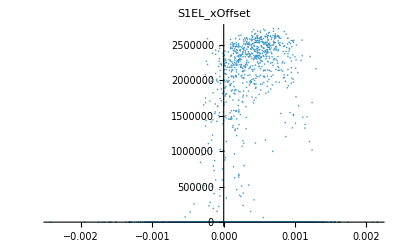
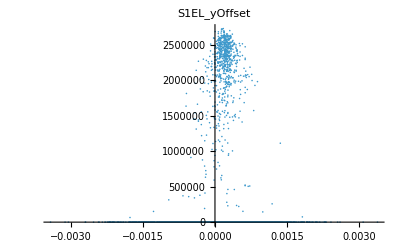
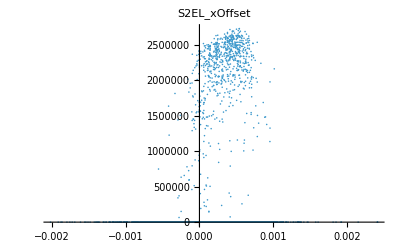
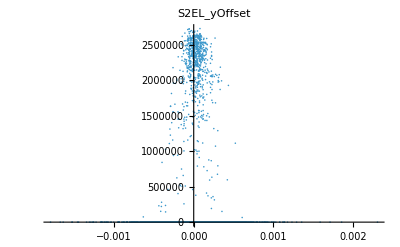
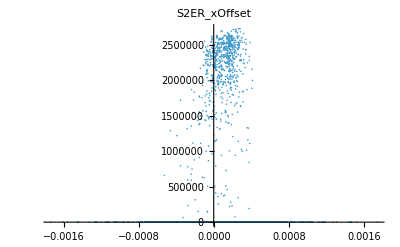
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

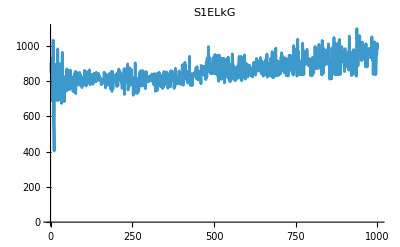
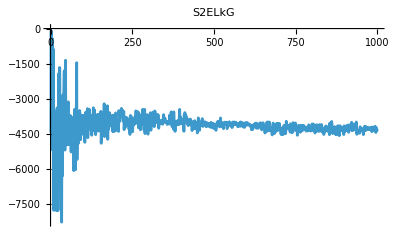
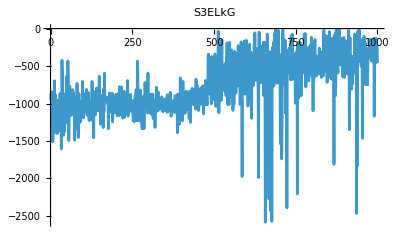
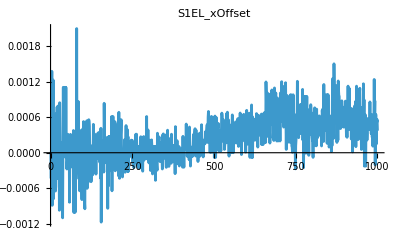
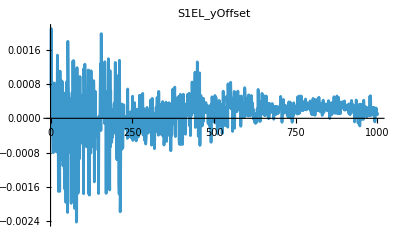
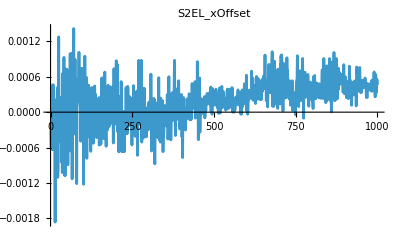
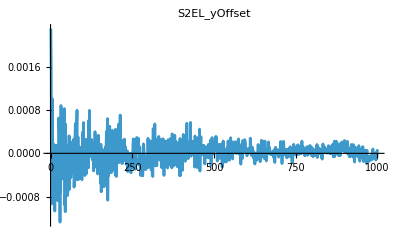
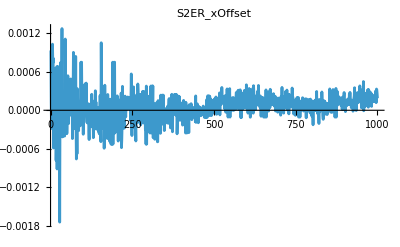
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Estimate maximizeMe asymptote

There’s no reason at all to think this is valid

```mathematica
(*runningBest = #["maximizeMe"]&/@raw;*)
```

```mathematica
Button["Calculate",

expr = a * Tanh[b ii]+c;
nlm=NonlinearModelFit[
Transpose[{Range[Length[runningBest]],runningBest}],
expr,
{
{a,Max[runningBest]},
{b,1/Length[runningBest]},
{c,Min[runningBest]}
},
ii,
Method->"NMinimize"
];

meanPredictionBands = nlm["MeanPredictionBands"];
singlePredictionBands = nlm["SinglePredictionBands"];
plotMe ={nlm["BestFit"]}~Join~meanPredictionBands~Join~singlePredictionBands;

img = Show[
ListPlot[
Transpose[{Range[Length[runningBest]],runningBest}],
PlotRange->{{0,Length[runningBest]*1.5},{0, Max[runningBest]*1.5}},
ImageSize->800
],

Plot[
plotMe,
{ii,0,Length[runningBest]*1.5},
PlotStyle->{{Opacity[0.5],Black},{Opacity[0.5],Red},{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Green}},
PlotRange->All
]

];

Print[
"Estimated limits: ",
Sort[
Limit[#,ii->Infinity]&/@plotMe
]
];
Print[img];
]
```

Calculate

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
(*Export[
"~/srData.csv",
Dataset[raw]
]*)
```

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | Missing[KeyAbsent,L1PhaseSet] | 20.312+Missing[KeyAbsent,L1PhaseSet]
L2PhaseSet | -38.6737 | Missing[KeyAbsent,L2PhaseSet] | 38.6737+Missing[KeyAbsent,L2PhaseSet]
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.000698704 | 0.000313449
S1EL_yOffset | -0.000241114 | 0.000173105 | 0.000414219
S2EL_xOffset | -0.00141787 | 0.000541028 | 0.0019589
S2EL_yOffset | 0.0000111705 | 0.0000786965 | 0.000067526
S2ER_xOffset | -0.00223816 | 0.000262815 | 0.00250098
S2ER_yOffset | -0.000675996 | -0.000149529 | 0.000526468
S1ER_xOffset | 0.00100714 | 0.000408866 | -0.000598271
S1ER_yOffset | 0.000398456 | -0.00089699 | -0.00129545
XC1FFkG | 0.206455 | 0.0565491 | -0.149906
XC3FFkG | -0.0899164 | -0.0301588 | 0.0597576
YC1FFkG | -0.0022312 | -0.00937079 | -0.00713959
YC2FFkG | -0.00851158 | 0.0664009 | 0.0749125